```mathematica
RestartTable:=List[{0,0},{1,3},{2,3}, {3,3}, {4,11}, {5,23}, {6,53},{7,107},{8,257}, {9, 457}]
```

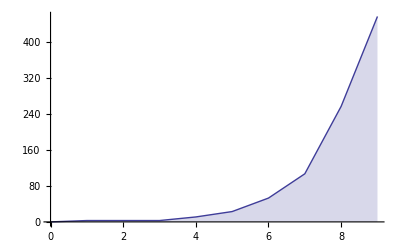

```mathematica
ListPlot[List[{0,0},{1,3},{2,3}, {3,3}, {4,11}, {5,23}, {6,53},{7,107},{8,257}, {9, 457}], Joined->True, Filling->Axis]
```

```mathematica
Jef[x_]:=InterpolatingPolynomial[{0, 11,23,53,107,191}, x]
```

```mathematica
Jef[13]
```

7205

748018821

17444

1563

-1199

-3087

InterpolatingFunction[{{3,0},{4,11},{5,23},{6,53},{7,107}}]

```mathematica
Table[Jef[i],{i,1,32}]
```

{0,11,23,53,107,191,322,539,914,1563,2657,4433,7205,11375,17444,26023,37844,53771,74811,102125,137039,181055,235862,303347,385606,484955,603941,745353,912233,1107887,1335896,1600127}

```mathematica
Table[Prime[i],{i,1,64}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311}

```mathematica
(179 181 191 193 197 199 211 223)^2
```

4853530979784243326730776411413955089

```mathematica
Definition[Jef[x]]
```

Definition::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Definition[Jef[x]].